## QM

### Diagonalizing

```mathematica
Sx=1/(√2){{0,1,0},{1,0,1},{0,1,0}};
Sy=1/(√2){{0,-ⅈ,0},{ⅈ,0,-ⅈ},{0,ⅈ,0}};
Sz={{1,0,0},{0,0,0},{0,0,-1}};
```

```mathematica
SxS=Table[SparseArray[Flatten[TensorProduct[IdentityMatrix[3^(n-1)],Sx,IdentityMatrix[3^(L-n)]],{{1,3,5},{2,4,6}}]],{n,1,L}];
SyS=Table[SparseArray[Flatten[TensorProduct[IdentityMatrix[3^(n-1)],Sy,IdentityMatrix[3^(L-n)]],{{1,3,5},{2,4,6}}]],{n,1,L}];SzS=Table[SparseArray[Flatten[TensorProduct[IdentityMatrix[3^(n-1)],Sz,IdentityMatrix[3^(L-n)]],{{1,3,5},{2,4,6}}]],{n,1,L}];
```

```mathematica
Dimensions[SzS]
```

{5,243,243}

```mathematica
Dimensions[Sz]
```

{3,3}

```mathematica
(*HQM=Sum[U/2 SzS[[n]].SzS[[n]]-μ SzS[[n]],{n,1,M}]- J navg Sum[Sum[SxS[[n]].SxS[[m]]+SyS[[n]].SyS[[m]],{m,n+1,M}],{n,1,M}];*)
```

```mathematica
ProgressIndicator[Dynamic[l],{1,L}]
```

```mathematica
ProgressIndicator[Dynamic[n],{1,L}]
```

```mathematica
ProgressIndicator[Dynamic[m],{1,L}]
```

```mathematica
Timing[HQM=Sum[1/2 SzS[[l]].SzS[[l]]- SzS[[l]],{l,1,L}]-Jx Sum[Sum[Flatten[TensorProduct[IdentityMatrix[3^(n-1)],Sx,IdentityMatrix[3^(m-n-1)],Sx,IdentityMatrix[3^(L-m)]],{{1,3,5,7,9},{2,4,6,8,10}}],{m,n+1,L}],{n,1,L}]-Jy Sum[Sum[Flatten[TensorProduct[IdentityMatrix[3^(n-1)],Sy,IdentityMatrix[3^(m-n-1)],Sy,IdentityMatrix[3^(L-m)]],{{1,3,5,7,9},{2,4,6,8,10}}],{m,n+1,L}],{n,1,L}];;]
```

{3.43845,Null}

```mathematica
HQM=1.*HQM;
```

```mathematica
(*Timing[{En,ψn}=Eigensystem[HQM];]*)
```

```mathematica
Timing[{En2,ψn2}=Eigensystem[HQM];]
```

{0.15909,Null}

```mathematica
ψn2=ψn2ᵀ;
```

### Initial conditions

```mathematica
allup2=Table[0,{3^L}];
allup2[[1]]=1;
```

```mathematica
cn2=ψn2†.allup2;
```

### Operator

```mathematica
RotSzS=1.*ψn2†.(Sum[SzS[[n]],{n,1,L}]).ψn2;
```

```mathematica
RotSz2=1.*ψn2†.(Sum[SzS[[n]].SzS[[n]],{n,1,L}]).ψn2;
```

```mathematica
AvgSzS=Table[0,{Nt}];
AvgSz2=Table[0,{Nt}];
Do[
vec2=1.*ⅇ^(-ⅈ times[[n]]En2)cn2;
AvgSzS[[n]]=Re[vec2*.RotSzS.vec2];
AvgSz2[[n]]=Re[vec2*.RotSz2.vec2];
,{n,1,Nt}]
```

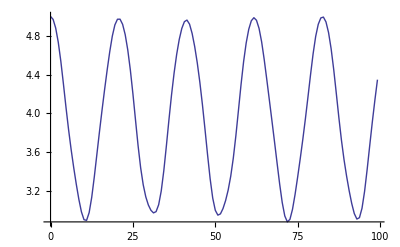

```mathematica
ListPlot[{times,AvgSzS}ᵀ,Joined->True]
```

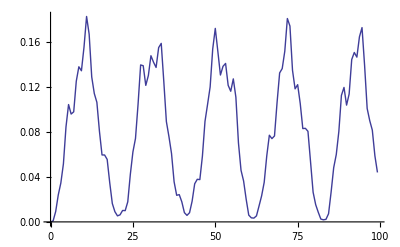

```mathematica
ListPlot[{times,AvgSz2-AvgSzS}ᵀ,Joined->True]
```